```mathematica
τ=1
σ=0.1
ρ=0.001
```

1

0.1

0.001

```mathematica
inte=1/Sqrt[2 π σ^2]((1-ρ)DiracDelta[x]+ρ/τ Exp[-x / τ]HeavisideTheta[x])Exp[-(x-R)^2/(2 σ^2)]
```

(ⅇ^(-(-R+x)^2/(2 σ^2)) ((1-ρ) DiracDelta[x]+(ⅇ^(-x/τ) ρ HeavisideTheta[x])/τ))/(√(2 π) √(σ^2))

```mathematica
Z=FullSimplify[Integrate[inte,{x,-1,Infinity}],σ>0]
```

-(ⅇ^(-R^2/(2 σ^2)) (-1+ρ))/(√(2 π) σ)+(ⅇ^((σ^2-2 R τ)/(2 τ^2)) ρ (1+Erf[(-σ+(R τ)/σ)/(√2 τ)]))/(2 τ)

```mathematica
fa = FullSimplify[R+σ^2/Z D[Z,R]]
```

(ⅇ^(R/τ) ρ σ (-√2 σ τ+ⅇ^((σ-(R τ)/σ)^2/(2 τ^2)) √π (σ^2-R τ) (1+Erf[(-σ+(R τ)/σ)/(√2 τ)])))/(τ (√2 ⅇ^(R/τ) (-1+ρ) τ+ⅇ^((R^2+σ^4/τ^2)/(2 σ^2)) √π ρ σ (-2+Erfc[(-σ+(R τ)/σ)/(√2 τ)])))

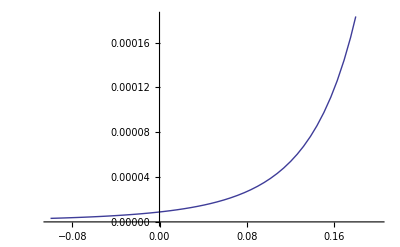

```mathematica
Plot[fa,{R,-0.1,0.2}]
```

```mathematica
FullSimplify[Integrate[Exp[-x/τ-(x-R)^2/(2 σ^2)],{x,0,Infinity}],σ>0]
```

ⅇ^((σ^2-2 R τ)/(2 τ^2)) √(π/2) σ (1+Erf[(-σ+(R τ)/σ)/(√2 τ)])

```mathematica
Simplify[Integrate[Exp[-(x-R)^2/2/σ^2]Exp[-x/τ],{x,0,+Infinity}],σ>0]
```

ⅇ^((σ^2-2 R τ)/(2 τ^2)) √(π/2) σ (1+Erf[(-σ+(R τ)/σ)/(√2 τ)])

```mathematica
D[Erf[x],x]
```

(2 ⅇ^(-x^2))/(√π)